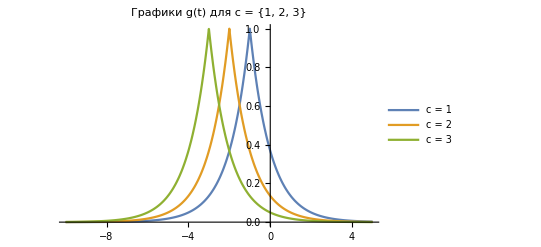

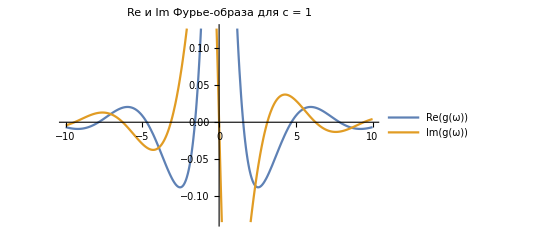
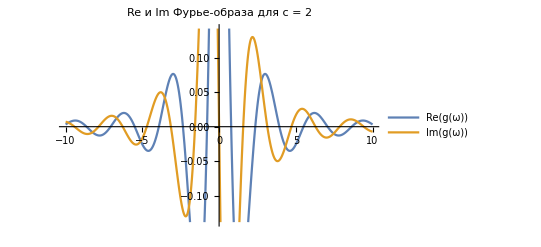
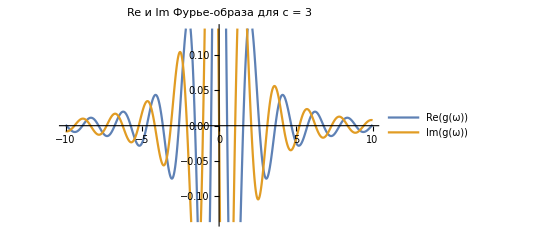

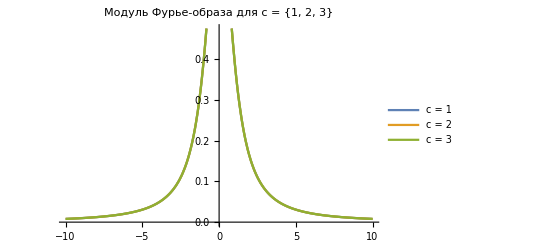

```mathematica
a=1;
b=1;
f[t_]:=a Exp[-b Abs[t]];

cValues={1,2,3};
g[t_,c_]:=f[t+c];

fourierTransforms=Table[FourierTransform[g[t,c],t,ω],{c,cValues}];

Plot[Evaluate[Table[g[t,c],{c,cValues}]],{t,-10,5},PlotLabel->"Графики g(t) для c = {1, 2, 3}",PlotLegends->Table["c = "<>ToString[c],{c,cValues}],PlotRange->{Automatic,{0,1}}]

plotsReIm=Table[Plot[{Re[fourierTransforms[[c]]],Im[fourierTransforms[[c]]]},{ω,-10,10},PlotLegends->{Style["Re(g(ω))",FontSize->20],Style["Im(g(ω))",FontSize->14]},PlotLabel->"Re и Im Фурье-образа для c = "<>ToString[cValues[[c]]]],{c,Length[cValues]}]

plotsAbs = Plot[Evaluate[Table[Abs[fourierTransforms[[c]]],{c,Length[cValues]}]],{ω,-10,10},PlotLabel->"Модуль Фурье-образа для c = {1, 2, 3}",PlotLegends->Table["c = "<>ToString[cValues[[c]]],{c,Length[cValues]}], PlotRange->{Automatic,{0,1}}]
```

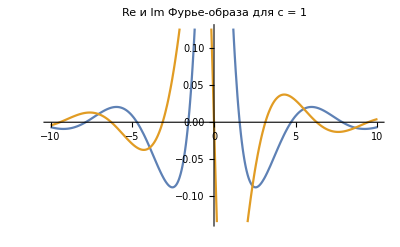
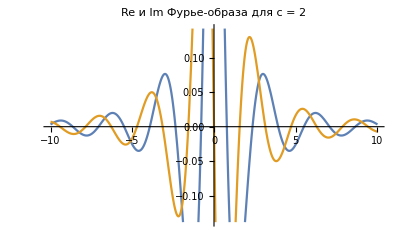
```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

-Graphics-